```mathematica
SetDirectory["/home/kn/Documents/thesis"]
```

/home/kn/Documents/thesis

```mathematica
"/home/kn/Documents/thesis"
```

```mathematica
data = Import["XBTUSD-5m-data.csv",{"Data",All,6}]
data = Delete[data, 1]
```

{close,9499.5,9498.5,9493.,9511.,9498.,9498.5,9507.,9488.,9499.5,9494.5,9492.5,9487.5,9489.5,9480.5,9477.5,9478.5,9487.,9484.,52955,8596.,8607.,8601.,8605.5,8610.,8627.,8619.,8621.5,8616.5,8625.,8623.,8624.5,8624.,8638.,8646.5,8626.,8624.,8625.,8620.}
 |  |  |  |

{9499.5,9498.5,9493.,9511.,9498.,9498.5,9507.,9488.,9499.5,9494.5,9492.5,9487.5,9489.5,9480.5,9477.5,9478.5,9487.,9484.,9475.5,52954,8596.,8607.,8601.,8605.5,8610.,8627.,8619.,8621.5,8616.5,8625.,8623.,8624.5,8624.,8638.,8646.5,8626.,8624.,8625.,8620.}
 |  |  |  |

```mathematica
ClearAll[s,s1, θ, σ, κ, τ];
```

```mathematica
lPdf =Log[σ] + 1/(2*τ*σ^2)(2(Sqrt[s] - Sqrt[s1]) - τ/Sqrt[s1]*(κ*(θ - s1) - σ^2/4))^2
```

((2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))^2)/(2 σ^2 τ)+Log[σ]

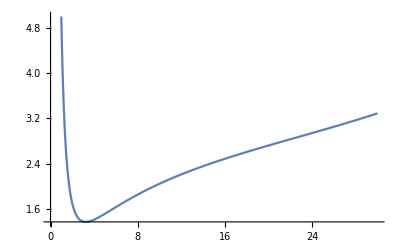

```mathematica
ClearAll[κ, σ]
θ = Mean[data];
s = data[[2]];
s1 = data[[1]];
κ = 5;
τ = 5/(365*24*60);
Plot[Log[σ*Sqrt[s]] + (x[s, σ] - x[s1, σ] - b[x[s1, σ], κ, θ,σ]*τ)^2/(2*τ) -Log[1/Sqrt[2*Pi*τ]], {σ, 0, 30}]
```

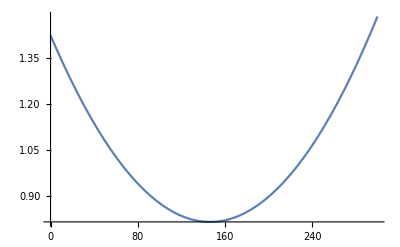

```mathematica
ClearAll[κ, σ]
θ = Mean[data];
s = data[[2]];
s1 = data[[1]];
σ = 3;
τ = 5/(365*24*60);
Plot[Log[σ*Sqrt[s]] + (x[s, σ] - x[s1, σ] - b[x[s1, σ], κ, θ,σ]*τ)^2/(2*τ) -Log[1/Sqrt[2*Pi*τ]], {κ, 0, 300}]
```

```mathematica
ClearAll[κ, σ]
θ = Mean[data];
s = data[[2]];
s1 = data[[1]];
τ = 5/(365*24*60);
Plot3D[Log[σ*Sqrt[s]] + (x[s, σ] - x[s1, σ] - b[x[s1, σ], κ, θ,σ]*τ)^2/(2*τ) -Log[1/Sqrt[2*Pi*τ]], {σ, 0, 30}, {κ, 0, 500}]
```

-Graphics3D-

```mathematica
gradF = D[lPdf, {{σ, θ, κ}}]
hess = D[lPdf, {{σ, θ, κ}, 2}]
```

{1/σ+(2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))/(2 √s1 σ)-((2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))^2)/(σ^3 τ),-(κ (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^2),-((-s1+θ) (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^2)}

{{-1/σ^2+τ/(4 s1)-(3 (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(2 √s1 σ^2)+(3 (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))^2)/(σ^4 τ),-(κ τ)/(2 s1 σ)+(2 κ (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^3),-((-s1+θ) τ)/(2 s1 σ)+(2 (-s1+θ) (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^3)},{-(κ τ)/(2 s1 σ)+(2 κ (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^3),(κ^2 τ)/(s1 σ^2),((-s1+θ) κ τ)/(s1 σ^2)-(2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))/(√s1 σ^2)},{-((-s1+θ) τ)/(2 s1 σ)+(2 (-s1+θ) (2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1)))/(√s1 σ^3),((-s1+θ) κ τ)/(s1 σ^2)-(2 (√s-√s1)-(((-s1+θ) κ-σ^2/4) τ)/(√s1))/(√s1 σ^2),((-s1+θ)^2 τ)/(s1 σ^2)}}

```mathematica
Needs["CCodeGenerator`"]
```

```mathematica
generateGradCCode[expr_, file_, header_] := 
Module[{i, cFuncs, funcNames},
cFuncs = List[];
funcNames = List[];
For[i=1, i≤Length[expr], i++, 
AppendTo[cFuncs, Compile[{{s, _Real}, {s1, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {τ, _Real}}, Evaluate[expr[[i]]]]];
AppendTo[funcNames, StringJoin["grad", ToString[i]]];
];
CCodeGenerate[cFuncs, funcNames,file,  "CodeTarget"->"WolframRTL"];
CCodeGenerate[cFuncs, funcNames, header, "CodeTarget"-> "WolframRTLHeader"];
];

generateHessCCode [expr_, file_, header_] := 
Module[{i, j, cFuncs, funcNames},
cFuncs = List[];
funcNames = List[];
For[i=1, i≤Dimensions[expr][[1]], i++,
For[j=1, j≤i, j++,
AppendTo[cFuncs, Compile[{{s, _Real}, {s1, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {τ, _Real}}, Evaluate[expr[[i,j]]]]];
AppendTo[funcNames, StringJoin["hess", ToString[i],"_", ToString[j]]];
];
CCodeGenerate[cFuncs, funcNames,file,  "CodeTarget"->"WolframRTL"];
CCodeGenerate[cFuncs, funcNames, header, "CodeTarget"-> "WolframRTLHeader"];
];
];
```

```mathematica
generateGradCCode[gradF, "grad.c", "grad.h"]
generateHessCCode[hess, "hess.c", "hess.h"]
```

```mathematica
cLPdf = Compile[{{s, _Real}, {s1, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {τ, _Real}}, Evaluate[lPdf]];
```

```mathematica
CCodeGenerate[cLPdf, "model", "model.c", "CodeTarget"->"WolframRTL"];
CCodeGenerate[cLPdf, "model", "model.h", "CodeTarget"->"WolframRTLHeader"];
```

```mathematica
σ = 0.3;
θ = Mean[data];
κ = 5;
s = data[[2]];
s1 = data[[1]];
τ = 5/(365*24*60);
gradF[[3]]
h = 10^-6;
κ = κ + h;
gradApx = lPdf;
κ = κ - h;
gradApx -= lPdf;
gradApx /= h
```